Fitting Gaussians to Modified Woods-Saxon Potential

defining global constants

```mathematica
DIFFUSIVITY=0.6;
R0 = 1.2; (*[fm]*)
Ac = 10; (*number of core nucleons*)
J = 0.5; (*total angular momentum*)
l = 1;  (*orbital angular momentum*)
VLS = -21; (*[MeV]*)
rEps = 0.00001;(*small r parameter*)

rVals = Subdivide[1.*^-5, 15, 10000];
V0 = (-11.39)*(-1)^l - 51.13;
Rcore = R0*Ac^(1/3);
```

defining functions

```mathematica
(*generate the geometric betas for use in our gaussians
NOTE: the success of this method is VERY dependent on the initial values of r1 and a!! good choices seem to be a=1.4ish for l=0, and a=1.3ish for l=1. i figure this out by finding the maximum difference between our estimated gaussian potential and the real woods-saxon later (once the curve fit has been done), and choosing an a which makes this small. there is Absolutely a better more numeric way to pick a but this works for now so i'm sticking with it
*)
generateBetas[numGaussians_Integer, r1_: 1.8, a_: 1.4] :=  Module[
{rn},
rn = Table[r1*a^i, {i, 0, numGaussians - 1}];
  1/(rn^2)
];
```

add the functions to define the woods-saxon potential without the spin-orbit correction

```mathematica
noSpinOrbitPotential[rList_List, orbAng_: l, diffusivity_: DIFFUSIVITY, 
   r0_: R0, numCoreNucleons_: Ac] :=Module[
{V0, Rcore},
  V0 = (-11.39)*(-1)^orbAng - 51.13;
  Rcore = r0*numCoreNucleons^(1/3);
  V0/(Exp[(rList - Rcore)/diffusivity] + 1)
 ];

analyticWS = noSpinOrbitPotential[rVals];
```

calculate the spin-orbit term and add it to our analytic potential

```mathematica
(*calculate the derivative for use in the spin-orbit term*)
expTerm = Exp[(rVals - Rcore)/DIFFUSIVITY];
centralWS = V0/(expTerm + 1);
dcentralDR = V0*(-(1/DIFFUSIVITY)*expTerm/(expTerm + 1)^2);

(*add a spin-orbit term complete with a smooth regularisation when r tends to zero
this method inspired by this phd thesis i found: https://math.ucr.edu/home/baez/physical/sarang_gopalakrishnan_thesis.pdf (mentions in the introduction that smoothing fixes most problems caused by r blowing up near zero, would probs have to check this more thoroughly for woods-saxon applications but it seems to work here?)
*)
invRSmooth[r_] := r/(r^2 + rEps^2);  (*goes to 0 as r->0, ~1/r for r >> rEps*)
invRVec = invRSmooth /@ rVals;(*applying this to our r values array from earlier*)

Print["rEps = ",rEps];
Print["invRVec min,max = ",Min[invRVec],", ",Max[invRVec]];

spinCouplingTerm = ((J*(J + 1))/2) - ((l*(l + 1))/2) - 0.375;

(*Analytic WS including spin-orbit*)
analyticWSwithSO = centralWS - VLS*invRVec *spinCouplingTerm*dcentralDR;
```

rEps = 0.00001

invRVec min,max = 0.0666667, 50000.

perform gaussian fit to analytic woods saxon potential

NOTE 1:
curve fit in any language will struggle here due to the very wide range of r values used (we need to start as close to r=0 as possible to get a fit which works to estimate ground state eigenvalues - this means we need to evaluate over loads of orders of magnitude of r)

basically i tried to do a normal curve fit on here and it did okay but the output function oscillated around the real woods-saxon potential and it wasn’t giving params that worked in our python wavefunction building code, researched this a bit and i think it’s because our curve fit problem was very ill conditioned

i did a massive deep dive into statistics and linear regression to try and fix this and found that ridge regression might do a good job of curve fitting! essentially (i think) because we have such a fat range in r, curve fit could find loads of possible solutions - two gaussians with very different betas can overlap to define parts of the function, especially in small r, and that’s why curve fit struggles and is v numerically unstable (and makes gaussians that are the same or cancel each other out thank you scipy curvefit).

doing ridge regression seems to mitigate this - from what i understand you add a penalty term proportional to the magnitude of the curvefit param to stop the curve fit from picking param values which are absolutely insane orders of magnitude lol. in practise this means adding a term $lambda * sum_j{c_j^2}*$ to the least squares equation and minimising that (lambda is just some constant). this will also reduce the variance on the parameters a bit (do not ask me how that works i don’t know the maths lol). ridge regularisation will ensure that our overall fit will be smooth and have good behaviour for all r (at the cost of a slightly less precise fit to the woods-saxon, but you will see that it seems to match up well enough lol)

this source explains the maths behind ridge regression: https://online.stat.psu.edu/stat857/node/155/

NOTE 2:
i also implemented something called column scaling (also called standardisation) - also found this on a stats deep dive and it is supposed to improve the numerical instability of our answers (so we don’t have to be exactly right and copy jagjit on our estimation of the gaussian initial parameters)

when we do a least squares fit we generate a matrix of the predicted function - our real function for each given parameter we are fitting (aka a 12x12 square matrix for our 12 gaussians). when doing the curve-fit, the values in some of the matrix columns will be WAY bigger than other columns (especially for our range of r vals) and it will cause numerical instability and potentially really big condition numbers (which you can apparently use analogous to our eigenvalues in order to characterise how good the params are yippee!).

so column scaling just means to divide each column by its norm so that each gaussian basis function has roughly the same scale and will be treated equally in the curve fit (stops everything converging to 12 copies of a single gaussian like we saw in the python attempt)

this source explains things a bit better (we use the standard deviation normalisation here, i read a couple of sources explaining why this one was good but i accidentally closed them when i shut down my pc sorry! working on getting them back now but the code does work so i guess it was justified lol): https://www.listendata.com/2017/04/how-to-standardize-variable-in-regression.html

i am currently working on putting more detailed (mathsy) descriptions in my overleaf notes so we can both use them

```mathematica
betas2 = generateBetas[2];
betas12 = generateBetas[12];

(*add the design matrix which represents the least squares problem (without any ridge regression yet!*)
designMatrix[rList_, betas_] := 
  Transpose[Table[Exp[-betas[[i]]*rList^2], {i, Length[betas]}]];

(*do the curvefit using ridge regression, adding column scaling*)
ridgeSolve[designMatrix_,targetVector_,lambda_:1.*^-6]:=Module[
{X=designMatrix,y=targetVector,numSamples,numFeatures,columnNorms,Xscaled,identityMat,normalMatrix,rhs,scaledCoeffs,coeffs}(*renaming things so i don't have to type all these words every time
designMatrix (x) is our matrix of gaussians which we wanna converge towards our WS
targetVector (y) is what we wanna fit to (in this case our analytic WS)
lambda is related to the penalty term for having weirdly large coefficients - i picked small numbers for this and it seemed to work ok
numSamples is the number of r values
numFeatures is the numer of parameters to be curve fitted
*),

{numSamples,numFeatures}=Dimensions[X];

(*do column scaling - find norm of each column*)columnNorms=Table[If[Norm[X[[All,j]]]==0,1.,Norm[X[[All,j]]]],{j,numFeatures}];
(*normalise columns so each has norm=1*)
Xscaled=Transpose[Transpose[X]/columnNorms];

(*do the curvefit with the ridge regression term added*)
identityMat=IdentityMatrix[numFeatures];
normalMatrix=Transpose[Xscaled].Xscaled;
rhs=Transpose[Xscaled].y;(*mathematica LinearSolve solves linear system of equations generated by our regression equation*)
scaledCoeffs=LinearSolve[normalMatrix+lambda*identityMat,rhs];(*divide coefficients by the norm of each column to undo the column scaling we did earlier and get the true params!*)
coeffs=scaledCoeffs/columnNorms;
coeffs
];

(*do the curve fit to the woods-saxon without any spin orbit term added*)
design2 = designMatrix[rVals, betas2];
design12 = designMatrix[rVals, betas12];
bvec = analyticWS / V0(*just divided by V0 for clarity so i don't get confused about whether the coefficients have been scaled by V0 or not lol*);

coeffs2 = ridgeSolve[design2, bvec, 1.*^-8];
coeffs12 = ridgeSolve[design12, bvec, 1.*^-6];
Print[coeffs2];
Print[coeffs12];

(*put them V0s back in to get the gaussians yippee!*)
fittedTwoBasic = V0*(design2 . coeffs2);
fittedTwelveBasic = V0*(design12 . coeffs12);
```

{-0.659952,1.65959}

{-1.32026,3.17779,-1.45976,0.979,-0.677651,0.342524,0.0693199,-0.145809,-0.10627,-0.0186357,0.0466222,0.0855406}

now compute derivatives of the gaussian fits in order to obtain a fit to the modified woods-saxon with the spin-orbit added

```mathematica
(*derivative of all the terms in the linear regression design matrix (i.e. the matrix of gaussians)*)
designDeriv[rList_, betas_] := 
  Transpose[Table[-2*betas[[i]]*rList*Exp[-betas[[i]]*rList^2], {i, Length[betas]}]];

dVdr2 = V0*(designDeriv[rVals, betas2] . coeffs2);
dVdr12 = V0*(designDeriv[rVals, betas12] . coeffs12);

dVdrOverR2 = dVdr2*invRVec;
dVdrOverR12 = dVdr12*invRVec;

spinTermTwo = VLS*spinCouplingTerm*dVdrOverR2;
spinTermTwelve = VLS*spinCouplingTerm*dVdrOverR12;

correctedTwo = fittedTwoBasic - spinTermTwo;
correctedTwelve = fittedTwelveBasic - spinTermTwelve;

(*print the maximum difference over all r between our fit and the real-woods saxon potential
am using this now to characterise the goodness of the fit we can do something more rigorous later*)
(*Print["Max difference analytic WS vs corrected 2-Gauss: ", 
  Max[Abs[analyticWSwithSO - correctedTwo]]];
Print["Max difference analytic WS vs corrected 12-Gauss: ", 
  Max[Abs[analyticWSwithSO - correctedTwelve]]];*)
```

plot everything!
NOTE:
i have no idea how plotting works on mathematica so they’re a bit scuffed but you kinda get the picture, will fix this later

```mathematica
(*do a safe logarithm, copes if the logarithm is undefined (aka if our fit sucked and there are regions of positive potential, this was kicking my ass earlier and i couldn't see any graphs*)
safeLog[list_] := Map[If[# < 0, Log[-#], Indeterminate] &, list];

p1 = ListLinePlot[{Transpose[{rVals, analyticWS}], 
    Transpose[{rVals, fittedTwoBasic}]},
   PlotLegends -> {"Analytic WS (no SO)", "2-Gauss Fit"},
   PlotRange -> All, AxesLabel -> {"r (fm)", "V(r) (MeV)"}];

p2 = ListLinePlot[{Transpose[{rVals, safeLog[analyticWS]}], 
    Transpose[{rVals, safeLog[fittedTwoBasic]}]},
   PlotLegends -> {"ln(-Analytic WS)", "ln(-2-Gauss Fit)"},
   PlotRange -> All, AxesLabel -> {"r (fm)", "ln(-V)"}];

p3 = ListLinePlot[{Transpose[{rVals, analyticWSwithSO}], 
    Transpose[{rVals, correctedTwelve}]},
   PlotLegends -> {"Analytic WS with SO", "2-Gauss Corrected"},
   PlotRange -> All, AxesLabel -> {"r (fm)", "V(r) (MeV)"}];

p4 = ListLinePlot[{Transpose[{rVals, safeLog[analyticWSwithSO]}], 
    Transpose[{rVals, safeLog[correctedTwelve]}]},
   PlotLegends -> {"ln(-Analytic WS with SO)", "ln(-2-Gauss Corrected)"},
   PlotRange -> All, AxesLabel -> {"r (fm)", "ln(-V)"}];

GraphicsGrid[{{p1, p2}, {p3, p4}}]-Graphics-
```

-Graphics- -Graphics-

### fitting SUSY potential

```mathematica
susyData = Import["C:\\Users\\ellab\\Documents\\uni\\year 5\\halo nuclei\\sem 2\\week 7\\susy_potential_data.csv", "CSV"];
rVals = susyData[[All,1]];
susyVals = susyData[[All, 2]];
```

```mathematica
susyN=1000;

susyBetas = generateBetas[susyN, 0.004, 1.01];
susyDesign=designMatrix[rVals, susyBetas];
λ = 10^-8;
susyCoeffs = LinearSolve[Transpose[susyDesign].susyDesign + λ IdentityMatrix[susyN], Transpose[susyDesign].(susyVals/V0)];
susyFitted = V0 * (susyDesign.susyCoeffs);
susyMaxError = Max[Abs[susyVals - susyFitted]];
Print[susyMaxError];
```

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {«1»} may contain significant numerical errors.

70.573

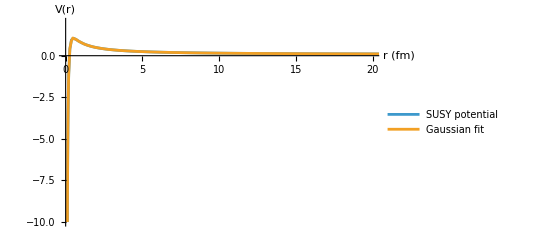

```mathematica
ListLinePlot[{Transpose[{rVals, susyVals}], Transpose[{rVals, susyFitted}]},
	PlotLegends -> {"SUSY potential", "Gaussian fit"},
	AxesLabel -> {"r (fm)", "V(r)"}, MaxPlotPoints -> 1000, PlotRange -> {{0, 20}, {-10, 2}}]
```